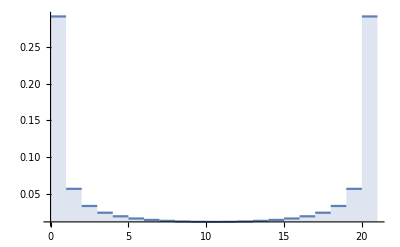

```mathematica
DiscretePlot[(0.5(PDF[BetaBinomialDistribution[α,β,20],x]/.{α -> 0.2, β -> 1.8 })+0.5(PDF[BetaBinomialDistribution[α,β,20],x]/.{α -> 1.8, β -> 0.2 })),{x,0,20},ExtentSize->Right, PlotRange->Full ]
```

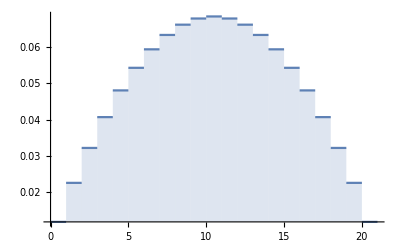

```mathematica
DiscretePlot[(0.5(PDF[BetaBinomialDistribution[α,β,20],x]/.{α -> 2, β -> 2 })+0.5(PDF[BetaBinomialDistribution[α,β,20],x]/.{α -> 2, β -> 2 })),{x,0,20},ExtentSize->Right, PlotRange->Full ]
```

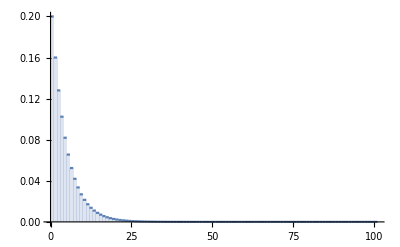

```mathematica
DiscretePlot[(PDF[NegativeBinomialDistribution[n,p],x]/.{n -> 1, p -> 0.2  }),{x,0,100},ExtentSize->Right, PlotRange->Full ]
```